```mathematica
FR$Parallel=False;
$FeynRulesPath=SetDirectory["/home/yoxara/feynrules-current"];
<<FeynRules`
SetDirectory[NotebookDirectory[]];
LoadModel["/home/yoxara/smodels/SmodelSSMS/2MDM/Feynrules/2MDM/2MDMnlo.fr"];
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

Yoxara Villamizar

Model Version: 1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model 2MDMnlo loaded.

```mathematica
(*CheckHermiticity[L2MDM,FlavorExpand->True]*)
```

```mathematica
vertices=FeynmanRules[L2MDM];(*,Exclude4Scalars->True*)
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

157 possible non-zero vertices have been found -> starting the computation:  / 157.

152 vertices obtained.

```mathematica
(*FeynmanRules[L2MDM,FlavorExpand->True]*)
```

```mathematica
decays=Simplify[ComputeWidths[vertices]]
```

Flavor expansion of the vertices:  / 152

Computing the squared matrix elements relevant for the 1->2 decays:

/ 72

{{{H1,H2,H2},(√(MH1^4-4 MH1^2 MH2^2) (Ca^3 lam3 vev+2 Ca (3 lam1-lam3) Sa^2 vev+2 Ca^2 (-3 lam2+lam3) Sa xev-lam3 Sa^3 xev)^2)/(32 π Abs[MH1]^3)},{{H2,H1,H1},(√(-4 MH1^2 MH2^2+MH2^4) (2 Ca^2 (3 lam1-lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev+2 Ca (3 lam2-lam3) Sa^2 xev)^2)/(32 π Abs[MH2]^3)},{{H2,chi^-,chi^-},(Ca^2 (-4 MchiT^2+MH2^2) √(-4 MchiT^2 MH2^2+MH2^4) ychi^2)/(32 π Abs[MH2]^3)},{{H1,chi^-,chi^-},((-4 MchiT^2+MH1^2) √(-4 MchiT^2 MH1^2+MH1^4) Sa^2 ychi^2)/(32 π Abs[MH1]^3)},{{H1,d,d^-},(3 Ca^2 (-4 MD^2+MH1^2) √(-4 MD^2 MH1^2+MH1^4) ydo^2)/(16 π Abs[MH1]^3)},{{H1,s,s^-},(3 Ca^2 (MH1^2-4 MS^2) √(MH1^4-4 MH1^2 MS^2) ys^2)/(16 π Abs[MH1]^3)},{{H1,b,b^-},(3 Ca^2 (-4 MB^2+MH1^2) √(-4 MB^2 MH1^2+MH1^4) yb^2)/(16 π Abs[MH1]^3)},{{H2,d,d^-},(3 (-4 MD^2+MH2^2) √(-4 MD^2 MH2^2+MH2^4) Sa^2 ydo^2)/(16 π Abs[MH2]^3)},{{H2,s,s^-},(3 (MH2^2-4 MS^2) √(MH2^4-4 MH2^2 MS^2) Sa^2 ys^2)/(16 π Abs[MH2]^3)},{{H2,b,b^-},(3 (-4 MB^2+MH2^2) √(-4 MB^2 MH2^2+MH2^4) Sa^2 yb^2)/(16 π Abs[MH2]^3)},{{H1,e,e^-},(Ca^2 (-4 Me^2+MH1^2) √(-4 Me^2 MH1^2+MH1^4) ye^2)/(16 π Abs[MH1]^3)},{{H1,mu,mu^-},(Ca^2 (MH1^2-4 MMU^2) √(MH1^4-4 MH1^2 MMU^2) ym^2)/(16 π Abs[MH1]^3)},{{H1,ta,ta^-},(Ca^2 (MH1^2-4 MTA^2) √(MH1^4-4 MH1^2 MTA^2) ytau^2)/(16 π Abs[MH1]^3)},{{H2,e,e^-},((-4 Me^2+MH2^2) √(-4 Me^2 MH2^2+MH2^4) Sa^2 ye^2)/(16 π Abs[MH2]^3)},{{H2,mu,mu^-},((MH2^2-4 MMU^2) √(MH2^4-4 MH2^2 MMU^2) Sa^2 ym^2)/(16 π Abs[MH2]^3)},{{H2,ta,ta^-},((MH2^2-4 MTA^2) √(MH2^4-4 MH2^2 MTA^2) Sa^2 ytau^2)/(16 π Abs[MH2]^3)},{{H1,u,u^-},(3 Ca^2 (MH1^2-4 MU^2) √(MH1^4-4 MH1^2 MU^2) yup^2)/(16 π Abs[MH1]^3)},{{H1,c,c^-},(3 Ca^2 (-4 MC^2+MH1^2) √(-4 MC^2 MH1^2+MH1^4) yc^2)/(16 π Abs[MH1]^3)},{{H1,t,t^-},(3 Ca^2 (MH1^2-4 MT^2) √(MH1^4-4 MH1^2 MT^2) yt^2)/(16 π Abs[MH1]^3)},{{H2,u,u^-},(3 (MH2^2-4 MU^2) √(MH2^4-4 MH2^2 MU^2) Sa^2 yup^2)/(16 π Abs[MH2]^3)},{{H2,c,c^-},(3 (-4 MC^2+MH2^2) √(-4 MC^2 MH2^2+MH2^4) Sa^2 yc^2)/(16 π Abs[MH2]^3)},{{H2,t,t^-},(3 (MH2^2-4 MT^2) √(MH2^4-4 MH2^2 MT^2) Sa^2 yt^2)/(16 π Abs[MH2]^3)},{{H1,W^†,W},(Ca^2 e^4 √(MH1^4-4 MH1^2 M_W^2) (MH1^4-4 MH1^2 M_W^2+12 M_W^4) vev^2)/(256 M_W^4 π s_w^4 Abs[MH1]^3)},{{H2,W^†,W},(e^4 √(MH2^4-4 MH2^2 M_W^2) (MH2^4-4 MH2^2 M_W^2+12 M_W^4) Sa^2 vev^2)/(256 M_W^4 π s_w^4 Abs[MH2]^3)},{{Z,W^†,W},(c_w^2 e^2 √(-4 M_W^2 MZ^2+MZ^4) (-48 M_W^6-68 M_W^4 MZ^2+16 M_W^2 MZ^4+MZ^6))/(192 M_W^4 π s_w^2 Abs[MZ]^3)},{{H1,Z,Z},(Ca^2 e^4 √(MH1^4-4 MH1^2 MZ^2) (MH1^4-4 MH1^2 MZ^2+12 MZ^4) (c_w^2+s_w^2)^4 vev^2)/(512 c_w^4 MZ^4 π s_w^4 Abs[MH1]^3)},{{H2,Z,Z},(e^4 √(MH2^4-4 MH2^2 MZ^2) (MH2^4-4 MH2^2 MZ^2+12 MZ^4) Sa^2 (c_w^2+s_w^2)^4 vev^2)/(512 c_w^4 MZ^4 π s_w^4 Abs[MH2]^3)},{{H2,Zp,Zp},(Ca^2 g_chi^4 g_Zp^4 √(MH2^4-4 MH2^2 MZp^2) (MH2^4-4 MH2^2 MZp^2+12 MZp^4) xev^2)/(2 MZp^4 π Abs[MH2]^3)},{{H1,Zp,Zp},(g_chi^4 g_Zp^4 √(MH1^4-4 MH1^2 MZp^2) (MH1^4-4 MH1^2 MZp^2+12 MZp^4) Sa^2 xev^2)/(2 MZp^4 π Abs[MH1]^3)},{{W,u,d^-},-(CKM1x1 e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)) CKM1x1^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{d,W^†,u},(CKM1x1 e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)) CKM1x1^*)/(64 M_W^2 π s_w^2 Abs[MD]^3)},{{W,u,s^-},-(CKM1x2 e^2 (MS^4+MU^4+MU^2 M_W^2-2 M_W^4+MS^2 (-2 MU^2+M_W^2)) √(MS^4+(MU^2-M_W^2)^2-2 MS^2 (MU^2+M_W^2)) CKM1x2^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{s,W^†,u},(CKM1x2 e^2 (MS^4+MU^4+MU^2 M_W^2-2 M_W^4+MS^2 (-2 MU^2+M_W^2)) √(MS^4+(MU^2-M_W^2)^2-2 MS^2 (MU^2+M_W^2)) CKM1x2^*)/(64 M_W^2 π s_w^2 Abs[MS]^3)},{{W,u,b^-},-(CKM1x3 e^2 (MB^4+MU^4+MU^2 M_W^2-2 M_W^4+MB^2 (-2 MU^2+M_W^2)) √(MB^4+(MU^2-M_W^2)^2-2 MB^2 (MU^2+M_W^2)) CKM1x3^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,u},(CKM1x3 e^2 (MB^4+MU^4+MU^2 M_W^2-2 M_W^4+MB^2 (-2 MU^2+M_W^2)) √(MB^4+(MU^2-M_W^2)^2-2 MB^2 (MU^2+M_W^2)) CKM1x3^*)/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{W,c,d^-},-(CKM2x1 e^2 (MC^4+MD^4+MD^2 M_W^2-2 M_W^4+MC^2 (-2 MD^2+M_W^2)) √(MC^4+(MD^2-M_W^2)^2-2 MC^2 (MD^2+M_W^2)) CKM2x1^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{d,W^†,c},(CKM2x1 e^2 (MC^4+MD^4+MD^2 M_W^2-2 M_W^4+MC^2 (-2 MD^2+M_W^2)) √(MC^4+(MD^2-M_W^2)^2-2 MC^2 (MD^2+M_W^2)) CKM2x1^*)/(64 M_W^2 π s_w^2 Abs[MD]^3)},{{W,c,s^-},-(CKM2x2 e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)) CKM2x2^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{s,W^†,c},(CKM2x2 e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)) CKM2x2^*)/(64 M_W^2 π s_w^2 Abs[MS]^3)},{{W,c,b^-},-(CKM2x3 e^2 (MB^4+MC^4+MC^2 M_W^2-2 M_W^4+MB^2 (-2 MC^2+M_W^2)) √(MB^4+(MC^2-M_W^2)^2-2 MB^2 (MC^2+M_W^2)) CKM2x3^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,c},(CKM2x3 e^2 (MB^4+MC^4+MC^2 M_W^2-2 M_W^4+MB^2 (-2 MC^2+M_W^2)) √(MB^4+(MC^2-M_W^2)^2-2 MB^2 (MC^2+M_W^2)) CKM2x3^*)/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{W,t,d^-},-(CKM3x1 e^2 (MD^4+MT^4+MT^2 M_W^2-2 M_W^4+MD^2 (-2 MT^2+M_W^2)) √(MD^4+(MT^2-M_W^2)^2-2 MD^2 (MT^2+M_W^2)) CKM3x1^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{d,W^†,t},(CKM3x1 e^2 (MD^4+MT^4+MT^2 M_W^2-2 M_W^4+MD^2 (-2 MT^2+M_W^2)) √(MD^4+(MT^2-M_W^2)^2-2 MD^2 (MT^2+M_W^2)) CKM3x1^*)/(64 M_W^2 π s_w^2 Abs[MD]^3)},{{W,t,s^-},-(CKM3x2 e^2 (MS^4+MT^4+MT^2 M_W^2-2 M_W^4+MS^2 (-2 MT^2+M_W^2)) √(MS^4+(MT^2-M_W^2)^2-2 MS^2 (MT^2+M_W^2)) CKM3x2^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{s,W^†,t},(CKM3x2 e^2 (MS^4+MT^4+MT^2 M_W^2-2 M_W^4+MS^2 (-2 MT^2+M_W^2)) √(MS^4+(MT^2-M_W^2)^2-2 MS^2 (MT^2+M_W^2)) CKM3x2^*)/(64 M_W^2 π s_w^2 Abs[MS]^3)},{{W,t,b^-},-(CKM3x3 e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)) CKM3x3^*)/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,t},(CKM3x3 e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)) CKM3x3^*)/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{u,W,d},(CKM1x1 e^2 (MD^4+MU^4+MU^2 M_W^2-2 M_W^4+MD^2 (-2 MU^2+M_W^2)) √(MD^4+(MU^2-M_W^2)^2-2 MD^2 (MU^2+M_W^2)) CKM1x1^*)/(64 M_W^2 π s_w^2 Abs[MU]^3)},{{c,W,d},(CKM2x1 e^2 (MC^4+MD^4+MD^2 M_W^2-2 M_W^4+MC^2 (-2 MD^2+M_W^2)) √(MC^4+(MD^2-M_W^2)^2-2 MC^2 (MD^2+M_W^2)) CKM2x1^*)/(64 M_W^2 π s_w^2 Abs[MC]^3)},{{t,W,d},(CKM3x1 e^2 (MD^4+MT^4+MT^2 M_W^2-2 M_W^4+MD^2 (-2 MT^2+M_W^2)) √(MD^4+(MT^2-M_W^2)^2-2 MD^2 (MT^2+M_W^2)) CKM3x1^*)/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{u,W,s},(CKM1x2 e^2 (MS^4+MU^4+MU^2 M_W^2-2 M_W^4+MS^2 (-2 MU^2+M_W^2)) √(MS^4+(MU^2-M_W^2)^2-2 MS^2 (MU^2+M_W^2)) CKM1x2^*)/(64 M_W^2 π s_w^2 Abs[MU]^3)},{{c,W,s},(CKM2x2 e^2 (MC^4+MS^4+MS^2 M_W^2-2 M_W^4+MC^2 (-2 MS^2+M_W^2)) √(MC^4+(MS^2-M_W^2)^2-2 MC^2 (MS^2+M_W^2)) CKM2x2^*)/(64 M_W^2 π s_w^2 Abs[MC]^3)},{{t,W,s},(CKM3x2 e^2 (MS^4+MT^4+MT^2 M_W^2-2 M_W^4+MS^2 (-2 MT^2+M_W^2)) √(MS^4+(MT^2-M_W^2)^2-2 MS^2 (MT^2+M_W^2)) CKM3x2^*)/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{u,W,b},(CKM1x3 e^2 (MB^4+MU^4+MU^2 M_W^2-2 M_W^4+MB^2 (-2 MU^2+M_W^2)) √(MB^4+(MU^2-M_W^2)^2-2 MB^2 (MU^2+M_W^2)) CKM1x3^*)/(64 M_W^2 π s_w^2 Abs[MU]^3)},{{c,W,b},(CKM2x3 e^2 (MB^4+MC^4+MC^2 M_W^2-2 M_W^4+MB^2 (-2 MC^2+M_W^2)) √(MB^4+(MC^2-M_W^2)^2-2 MB^2 (MC^2+M_W^2)) CKM2x3^*)/(64 M_W^2 π s_w^2 Abs[MC]^3)},{{t,W,b},(CKM3x3 e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)) CKM3x3^*)/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{W,ve,e^-},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{e,W^†,ve},(e^2 (Me^2-M_W^2)^2 (Me^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[Me]^3)},{{W,vm,mu^-},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{mu,W^†,vm},(e^2 (MMU^2-M_W^2)^2 (MMU^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MMU]^3)},{{W,vt,ta^-},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{ta,W^†,vt},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MTA]^3)},{{Z,u,u^-},(e^2 √(-4 MU^2 MZ^2+MZ^4) (-9 c_w^4 (MU^2-MZ^2)-6 c_w^2 (11 MU^2+MZ^2) s_w^2+(7 MU^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,c,c^-},(e^2 √(-4 MC^2 MZ^2+MZ^4) (-9 c_w^4 (MC^2-MZ^2)-6 c_w^2 (11 MC^2+MZ^2) s_w^2+(7 MC^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,t,t^-},(e^2 √(-4 MT^2 MZ^2+MZ^4) (-9 c_w^4 (MT^2-MZ^2)-6 c_w^2 (11 MT^2+MZ^2) s_w^2+(7 MT^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,d,d^-},(e^2 √(-4 MD^2 MZ^2+MZ^4) (-9 c_w^4 (MD^2-MZ^2)+6 c_w^2 (-7 MD^2+MZ^2) s_w^2+(-17 MD^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,s,s^-},(e^2 √(-4 MS^2 MZ^2+MZ^4) (-9 c_w^4 (MS^2-MZ^2)+6 c_w^2 (-7 MS^2+MZ^2) s_w^2+(-17 MS^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,b,b^-},(e^2 √(-4 MB^2 MZ^2+MZ^4) (-9 c_w^4 (MB^2-MZ^2)+6 c_w^2 (-7 MB^2+MZ^2) s_w^2+(-17 MB^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ve,ve^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vm,vm^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vt,vt^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,e,e^-},(e^2 √(-4 Me^2 MZ^2+MZ^4) (c_w^4 (-Me^2+MZ^2)-2 c_w^2 (5 Me^2+MZ^2) s_w^2+(7 Me^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,mu,mu^-},(e^2 √(-4 MMU^2 MZ^2+MZ^4) (c_w^4 (-MMU^2+MZ^2)-2 c_w^2 (5 MMU^2+MZ^2) s_w^2+(7 MMU^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ta,ta^-},(e^2 √(-4 MTA^2 MZ^2+MZ^4) (c_w^4 (-MTA^2+MZ^2)-2 c_w^2 (5 MTA^2+MZ^2) s_w^2+(7 MTA^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Zp,u,u^-},(√(-4 MU^2 MZp^2+MZp^4) (g_qA^2 (-4 MU^2+MZp^2)+g_q^2 g_Zp^2 (2 MU^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,c,c^-},(√(-4 MC^2 MZp^2+MZp^4) (g_qA^2 (-4 MC^2+MZp^2)+g_q^2 g_Zp^2 (2 MC^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,t,t^-},(√(-4 MT^2 MZp^2+MZp^4) (g_qA^2 (-4 MT^2+MZp^2)+g_q^2 g_Zp^2 (2 MT^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,d,d^-},(√(-4 MD^2 MZp^2+MZp^4) (g_qA^2 (-4 MD^2+MZp^2)+g_q^2 g_Zp^2 (2 MD^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,s,s^-},(√(-4 MS^2 MZp^2+MZp^4) (g_qA^2 (-4 MS^2+MZp^2)+g_q^2 g_Zp^2 (2 MS^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,b,b^-},(√(-4 MB^2 MZp^2+MZp^4) (g_qA^2 (-4 MB^2+MZp^2)+g_q^2 g_Zp^2 (2 MB^2+MZp^2)))/(4 π Abs[MZp]^3)},{{Zp,chi^-,chi^-},(g_chi^2 (-4 MchiT^2+MZp^2) √(-4 MchiT^2 MZp^2+MZp^4))/(24 π Abs[MZp]^3)}}

```mathematica
(*Simplify[TotWidth[Zp,decays]]*)
```

```mathematica
(*WriteLaTeXOutput[L2MDM,Output]*)
```

```mathematica
(*Decay_Zp*)
gqA = 0;
Zpuu =  FullSimplify[Collect[PartialWidth[{Zp, u, ubar},decays]/. MU^2->x*MZp^2,x,Simplify]]/. x->MU^2/MZp^2
Zpcc = FullSimplify[Collect[PartialWidth[{Zp, c, cbar},decays]/. MC^2->x*MZp^2,x,Simplify]]/. x->MC^2/MZp^2
Zptt =  FullSimplify[Collect[PartialWidth[{Zp, t, tbar},decays]/. MT^2->x*MZp^2,x,Simplify]]/. x->MT^2/MZp^2
Zpdd = FullSimplify[Collect[PartialWidth[{Zp, d, dbar},decays]/. MD^2->x*MZp^2,x,Simplify]]/. x->MD^2/MZp^2
Zpss = FullSimplify[Collect[PartialWidth[{Zp, s, sbar},decays]/. MS^2->x*MZp^2,x,Simplify]]/. x->MS^2/MZp^2
Zpbb = FullSimplify[Collect[PartialWidth[{Zp, b, bbar},decays]/. MB^2->x*MZp^2,x,Simplify]]/. x->MB^2/MZp^2
Zpdmdm =  FullSimplify[Collect[PartialWidth[{Zp, chibar, chibar},decays]/. MchiT^2->x*MZp^2,x,Simplify]]/. x->MchiT^2/MZp^2
```

(g_q^2 g_Zp^2 (1+(2 MU^2)/MZp^2) √((1-(4 MU^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_q^2 g_Zp^2 (1+(2 MC^2)/MZp^2) √((1-(4 MC^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_q^2 g_Zp^2 (1+(2 MT^2)/MZp^2) √((1-(4 MT^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_q^2 g_Zp^2 (1+(2 MD^2)/MZp^2) √((1-(4 MD^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_q^2 g_Zp^2 (1+(2 MS^2)/MZp^2) √((1-(4 MS^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_q^2 g_Zp^2 (1+(2 MB^2)/MZp^2) √((1-(4 MB^2)/MZp^2) MZp^4))/(4 √(MZp^2) π)

(g_chi^2 √((1-(4 MchiT^2)/MZp^2) MZp^4) (-4 MchiT^2+MZp^2))/(24 π Abs[MZp]^3)

```mathematica
H2uu = FullSimplify[Collect[PartialWidth[{H2, u, ubar},decays]/. MU^2->x*MH2^2,x,Simplify]]/. x->MU^2/MH2^2
StringReplace[ToString[H2uu,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2dd= FullSimplify[Collect[ PartialWidth[{H2, d, dbar},decays]/. MD^2->x*MH2^2,x,Simplify]]/. x->MD^2/MH2^2
StringReplace[ToString[H2dd,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2cc =   FullSimplify[Collect[PartialWidth[{H2, c, cbar},decays]/. MC^2->x*MH2^2,x,Simplify]]/. x->MC^2/MH2^2
StringReplace[ToString[H2cc,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2ss=  FullSimplify[Collect[PartialWidth[{H2, s, sbar},decays]/. MS^2->x*MH2^2,x,Simplify]]/. x->MS^2/MH2^2
StringReplace[ToString[H2ss,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2tt =FullSimplify[Collect[ PartialWidth[{H2, t, tbar},decays]/. MT^2->x*MH2^2,x,Simplify]]/. x->MT^2/MH2^2
StringReplace[ToString[H2tt,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2bb  =FullSimplify[Collect[ PartialWidth[{H2, b, bbar},decays]/. MB^2->x*MH2^2,x,Simplify]]/. x->MB^2/MH2^2
StringReplace[ToString[H2bb,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2dmdm =FullSimplify[Collect[PartialWidth[{H2, chibar, chibar},decays]/. MchiT^2->x*MH2^2,x,Simplify]]/. x->MchiT^2/MH2^2
StringReplace[ToString[H2dmdm,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2ee = FullSimplify[Collect[PartialWidth[{H2,e,ebar},decays]/. Me^2->x*MH2^2,x,Simplify]]/. x->Me^2/MH2^2
StringReplace[ToString[H2ee,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2mumu = FullSimplify[Collect[PartialWidth[{H2,mu, mubar},decays]/. MMU^2->x*MH2^2,x,Simplify]]/. x->MMU^2/MH2^2
StringReplace[ToString[H2mumu,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2tata=FullSimplify[Collect[ PartialWidth[{H2, ta, tabar},decays]/. MTA^2->x*MH2^2,x,Simplify]]/. x->MTA^2/MH2^2
StringReplace[ToString[H2tata,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2hh =FullSimplify[Collect[PartialWidth[{H2,H1,H1},decays] /. MH1^2->x*MH2^2,x,Simplify]]/. x->MH1^2/MH2^2
StringReplace[ToString[H2hh,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
ee=(2*MW*sw)/vev
H2ZZ = FullSimplify[Collect[ PartialWidth[{H2, Z, Z},decays]/. MZ^2->x*MH2^2,x,Simplify]]/. x->MZ^2/MH2^2
StringReplace[ToString[H2ZZ,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
H2WW =FullSimplify[Collect[  PartialWidth[{H2,Wbar, W},decays] /. MW^2->x*MH2^2,x,Simplify]]/. x->MW^2/MH2^2
StringReplace[ToString[H2WW,InputForm],{"Abs"->"abs","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
(*H2ZpZp=FullSimplify[Collect[(Subscript[c, α]^2 Subscript[g, sd]^4 Subscript[g, Zp]^4 √(Subscript[M, s]^4-4 Subscript[M, s]^2 MZp^2) (Subscript[M, s]^4-4 Subscript[M, s]^2 MZp^2+12 MZp^4) Subscript[υ, s]^2)/(32 MZp^4 π Abs[Subscript[M, s]]^3)/. MZp^2->x*Subscript[M, s]^2,x,Simplify]]/. x->MZp^2/Subscript[M, s]^2*)
```

(3 (MH2^2-4 MU^2) √(MH2^4 (1-(4 MU^2)/MH2^2)) Sa^2 yup^2)/(16 π Abs[MH2]^3)

(3*(MH2^2 - 4*MU^2)*sy.sqrt(MH2^4*(1 - (4*MU^2)/MH2^2))*Sa^2*yup^2)/(16*sy.pi*abs(MH2)^3)

(3 √((1-(4 MD^2)/MH2^2) MH2^4) (-4 MD^2+MH2^2) Sa^2 ydo^2)/(16 π Abs[MH2]^3)

(3*sy.sqrt((1 - (4*MD^2)/MH2^2)*MH2^4)*(-4*MD^2 + MH2^2)*Sa^2*ydo^2)/(16*sy.pi*abs(MH2)^3)

(3 √((1-(4 MC^2)/MH2^2) MH2^4) (-4 MC^2+MH2^2) Sa^2 yc^2)/(16 π Abs[MH2]^3)

(3*sy.sqrt((1 - (4*MC^2)/MH2^2)*MH2^4)*(-4*MC^2 + MH2^2)*Sa^2*yc^2)/(16*sy.pi*abs(MH2)^3)

(3 (MH2^2-4 MS^2) √(MH2^4 (1-(4 MS^2)/MH2^2)) Sa^2 ys^2)/(16 π Abs[MH2]^3)

(3*(MH2^2 - 4*MS^2)*sy.sqrt(MH2^4*(1 - (4*MS^2)/MH2^2))*Sa^2*ys^2)/(16*sy.pi*abs(MH2)^3)

(3 (MH2^2-4 MT^2) √(MH2^4 (1-(4 MT^2)/MH2^2)) Sa^2 yt^2)/(16 π Abs[MH2]^3)

(3*(MH2^2 - 4*MT^2)*sy.sqrt(MH2^4*(1 - (4*MT^2)/MH2^2))*Sa^2*yt^2)/(16*sy.pi*abs(MH2)^3)

(3 √((1-(4 MB^2)/MH2^2) MH2^4) (-4 MB^2+MH2^2) Sa^2 yb^2)/(16 π Abs[MH2]^3)

(3*sy.sqrt((1 - (4*MB^2)/MH2^2)*MH2^4)*(-4*MB^2 + MH2^2)*Sa^2*yb^2)/(16*sy.pi*abs(MH2)^3)

(Ca^2 √((1-(4 MchiT^2)/MH2^2) MH2^4) (-4 MchiT^2+MH2^2) ychi^2)/(32 π Abs[MH2]^3)

(Ca^2*sy.sqrt((1 - (4*MchiT^2)/MH2^2)*MH2^4)*(-4*MchiT^2 + MH2^2)*ychi^2)/(32*sy.pi*abs(MH2)^3)

(√((1-(4 Me^2)/MH2^2) MH2^4) (-4 Me^2+MH2^2) Sa^2 ye^2)/(16 π Abs[MH2]^3)

(sy.sqrt((1 - (4*Me^2)/MH2^2)*MH2^4)*(-4*Me^2 + MH2^2)*Sa^2*ye^2)/(16*sy.pi*abs(MH2)^3)

((MH2^2-4 MMU^2) √(MH2^4 (1-(4 MMU^2)/MH2^2)) Sa^2 ym^2)/(16 π Abs[MH2]^3)

((MH2^2 - 4*MMU^2)*sy.sqrt(MH2^4*(1 - (4*MMU^2)/MH2^2))*Sa^2*ym^2)/(16*sy.pi*abs(MH2)^3)

((MH2^2-4 MTA^2) √(MH2^4 (1-(4 MTA^2)/MH2^2)) Sa^2 ytau^2)/(16 π Abs[MH2]^3)

((MH2^2 - 4*MTA^2)*sy.sqrt(MH2^4*(1 - (4*MTA^2)/MH2^2))*Sa^2*ytau^2)/(16*sy.pi*abs(MH2)^3)

(√((1-(4 MH1^2)/MH2^2) MH2^4) (Ca^2 (6 lam1-2 lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev-2 Ca (-3 lam2+lam3) Sa^2 xev)^2)/(32 π Abs[MH2]^3)

(sy.sqrt((1 - (4*MH1^2)/MH2^2)*MH2^4)*(Ca^2*(6*lam1 - 2*lam3)*Sa*vev + lam3*Sa^3*vev + Ca^3*lam3*xev - 2*Ca*(-3*lam2 + lam3)*Sa^2*xev)^2)/(32*sy.pi*abs(MH2)^3)

(2 M_W s_w)/vev

-(M_W^4 √(MH2^4 (1-(4 MZ^2)/MH2^2)) (-12 MZ^4+MH2^4 (-1+(4 MZ^2)/MH2^2)) Sa^2 (c_w^2+s_w^2)^4)/(32 c_w^4 MZ^4 π vev^2 Abs[MH2]^3)

-1/32*(MW^4*sy.sqrt(MH2^4*(1 - (4*MZ^2)/MH2^2))*(-12*MZ^4 + MH2^4*(-1 + (4*MZ^2)/MH2^2))*Sa^2*(cw^2 + sw^2)^4)/(cw^4*MZ^4*sy.pi*vev^2*abs(MH2)^3)

(√(MH2^4 (1-(4 M_W^2)/MH2^2)) (12 M_W^4+MH2^4 (1-(4 M_W^2)/MH2^2)) Sa^2)/(16 π vev^2 Abs[MH2]^3)

(sy.sqrt(MH2^4*(1 - (4*MW^2)/MH2^2))*(12*MW^4 + MH2^4*(1 - (4*MW^2)/MH2^2))*Sa^2)/(16*sy.pi*vev^2*abs(MH2)^3)

```mathematica
(*lam1=MH1^2/(2*vev^2)*Ca^2+MH2^2/(2*vev^2)*Sa^2;
lam2=MH1^2/(2*xev^2)*Sa^2+MH2^2/(2*xev^2)*Ca^2;
lam3=(MH2^2-MH1^2)/(xev*vev)*Sa*Ca;*)
Ca = Cos[θ];
Sa = Sin[θ];
gchi = MZp/(2*xev)
lam1=(MH1^2+MH2^2+(MH1^2-MH2^2)*(Ca^2-Sa^2))/(4*vev^2)
lam2=(gchi^2*(MH1^2+MH2^2+(-MH1^2+MH2^2)*(Ca^2-Sa^2)))/MZp^2
lam3=(2*Ca*gchi*(MH1^2-MH2^2)*Sa)/(MZp*vev)
```

MZp/(2 xev)

(MH1^2+MH2^2+(MH1^2-MH2^2) (Cos[θ]^2-Sin[θ]^2))/(4 vev^2)

(MH1^2+MH2^2+(-MH1^2+MH2^2) (Cos[θ]^2-Sin[θ]^2))/(4 xev^2)

((MH1^2-MH2^2) Cos[θ] Sin[θ])/(vev xev)

```mathematica
PartialWidth[{H2,H1,H1},decays]
```

1/(128 π vev^2 xev^2 Abs[MH2]^3)√(MH2^2 (-4 MH1^2+MH2^2)) Cos[θ]^2 Sin[θ]^2 (3 MH1^2 xev Cos[θ]+3 MH2^2 xev Cos[θ]+5 MH1^2 xev Cos[θ]^3-5 MH2^2 xev Cos[θ]^3+3 MH1^2 vev Sin[θ]+3 MH2^2 vev Sin[θ]-7 MH1^2 vev Cos[θ]^2 Sin[θ]+7 MH2^2 vev Cos[θ]^2 Sin[θ]-7 MH1^2 xev Cos[θ] Sin[θ]^2+7 MH2^2 xev Cos[θ] Sin[θ]^2+5 MH1^2 vev Sin[θ]^3-5 MH2^2 vev Sin[θ]^3)^2

```mathematica
Whh = FullSimplify[Collect[PartialWidth[{H2,H1,H1},decays] /. MH1^2->x*MH2^2,x,Simplify]]/. x->MH1^2/MH2^2
```

(MH2 √((1-(4 MH1^2)/MH2^2) MH2^4) Cos[θ]^2 Sign[MH2]^3 Sin[θ]^2 ((1+(5 MH1^2)/MH2^2) xev Cos[θ]+3 (-1+MH1^2/MH2^2) xev Cos[3 θ]+(1+(5 MH1^2)/MH2^2) vev Sin[θ]-3 (-1+MH1^2/MH2^2) vev Sin[3 θ])^2)/(128 π vev^2 xev^2)

```mathematica
whh2 = FullSimplify[Collect[Whh,-1+MH1^2/MH2^2]]
```

1/(128 (MH2^2)^(3/2) π vev^2 xev^2)√(-4 MH1^2 MH2^2+MH2^4) Cos[θ]^2 Sin[θ]^2 ((5 MH1^2+MH2^2) xev Cos[θ]+3 (MH1-MH2) (MH1+MH2) xev Cos[3 θ]+(5 MH1^2+MH2^2) vev Sin[θ]-3 (MH1-MH2) (MH1+MH2) vev Sin[3 θ])^2

```mathematica
FullSimplify[Collect[whh2 /. MH1^2->x*MH2^2,x,Simplify]/. x->MH1^2/MH2^2]
```

1/(128 (MH2^2)^(3/2) π vev^2 xev^2)√(-4 MH1^2 MH2^2+MH2^4) Cos[θ]^2 Sin[θ]^2 ((5 MH1^2+MH2^2) xev Cos[θ]+3 (MH1-MH2) (MH1+MH2) xev Cos[3 θ]+(5 MH1^2+MH2^2) vev Sin[θ]-3 (MH1-MH2) (MH1+MH2) vev Sin[3 θ])^2

```mathematica
(*Ca = Cos[α];
Sa = Sin[α];
lam1=(1/(4*vev^2))*(MH2^2+MH1^2+(MH2^2-MH1^2)*(2*Ca^2-1));
lam2=(gchi^2/(MZp^2))*(MH2^2+MH1^2+(MH1^2-MH2^2)*(2*Ca^2-1));
lam3=2*qchi*(MH2^2-MH1^2)/(MZp*vev)*Sa*Ca;
mu2h=-lam1*vev^2-lam3/2*xev^2;
mu2sd=-lam3/2*vev^2-lam2*xev^2;
xev=MZp/(2*gchi)
gZp =1*)
(*qchi = MZp/(2*xev)*)
(*MZp 2*xev*qchi*)
```

```mathematica
(*cos[α]^2 sin[α]^2  is 1/4 sin^2[2α]*)
(*lam1=MH1^2/(2*vev^2)*Ca^2+MH2^2/(2*vev^2)*Sa^2;
lam2=MH1^2/(2*xev^2)*Sa^2+MH2^2/(2*xev^2)*Ca^2;
lam3=(MH2^2-MH1^2)/(xev*vev)*Sa*Ca;
mu2H1=-lam1*vev^2-lam3/2*xev^2;
mu2H2=-lam3/2*vev^2-lam2*xev^2;
Ca =cos[α];
Sa =sin[α];Mchi =(1/Sqrt[2])*ychi* xev;*)
```

```mathematica
(*PartialWidth[{H2, Zp, Zp},decays]
PartialWidth[{H1, d, dbar},decays]
PartialWidth[{H1, c, cbar},decays]
PartialWidth[{H1, s, sbar},decays]
PartialWidth[{H1, t, tbar},decays]
PartialWidth[{H1, b, bbar},decays]
PartialWidth[{H1, chi, chibar},decays]
BranchingRatio[{H2,chi,chibar},decays]
BranchingRatio[{Zp,chi,chibar},decays]*)
```

```mathematica
(*WriteLaTeXOutput[L2MDM,Output]*)
```

```mathematica
(*Expand[L2MDM];*)
```

```mathematica
Ca = Cos[θ];
Sa = Sin[θ];
lam1=(MH1^2+MH2^2+(MH1^2-MH2^2)*(Ca^2-Sa^2))/(4*vev^2);
lam2=(gchi^2*(MH1^2+MH2^2+(-MH1^2+MH2^2)*(Ca^2-Sa^2)))/MZp^2;
lam3=(2*Ca*gchi*(MH1^2-MH2^2)*Sa)/(MZp*vev);
Simplify[(2 Ca^2 (3 lam1-lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev+2 Ca (3 lam2-lam3) Sa^2 xev)]
```

1/(8 MZp^2 vev)(MZp (MH2^2 (3 MZp-2 gchi xev)+MH1^2 (9 MZp+2 gchi xev)) Cos[θ]+3 (MH1^2-MH2^2) MZp (MZp+2 gchi xev) Cos[3 θ]-4 gchi vev (MH1^2 (MZp-6 gchi xev)-MH2^2 (MZp+6 gchi xev)+3 (MH1^2-MH2^2) (MZp+2 gchi xev) Cos[2 θ]) Sin[θ]) Sin[2 θ]

```mathematica
FullSimplify[1/(8 MZp^2 vev)(MZp (MH2^2 (3 MZp-MZp)+MH1^2 (9 MZp+MZp)) Cos[θ]+3 (MH1^2-MH2^2) MZp (MZp+MZp) Cos[3 θ]-4 Subscript[g, chi] vev (MH1^2 (MZp-3MZp)-MH2^2 (MZp+3MZp)+3 (MH1^2-MH2^2) (MZp+MZp) Cos[2 θ]) Sin[θ]) Sin[2 θ]]
```

(Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MH2^2+3 (MH1-MH2) (MH1+MH2) Cos[2 θ])+vev ((5 MH1^2+MH2^2) Sin[θ]+3 (-MH1^2+MH2^2) Sin[3 θ]) g_chi))/(2 MZp vev)

```mathematica
3 (MH1-MH2) (MH1+MH2)
```

3 (MH1-MH2) (MH1+MH2)

```mathematica
Expand[3 (MH1-MH2) (MH1+MH2)]
```

3 MH1^2-3 MH2^2

```mathematica
(Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MH2^2+(3 MH1^2-3 MH2^2) Cos[2 θ])+vev ((5 MH1^2+MH2^2) Sin[θ]+3 (-MH1^2+MH2^2) Sin[3 θ]) Subscript[g, chi]))/(2 MZp vev)
```

(Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MH2^2+(3 MH1^2-3 MH2^2) Cos[2 θ])+vev ((5 MH1^2+MH2^2) Sin[θ]+3 (-MH1^2+MH2^2) Sin[3 θ]) g_chi))/(2 MZp vev)

```mathematica
FullSimplify[(Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MH2^2+(3 MH1^2-3 MH2^2) Cos[2 θ])+vev ((5 MH1^2+MH2^2) Sin[θ]+3 (-MH1^2+MH2^2) Sin[3 θ]) Subscript[g, chi]))/(2 MZp vev)]
```

```mathematica
FullSimplify[Collect[(Sin[2 θ] (MZp Cos[θ] (MH1^2+2 MH2^2+(3 MH1^2-3 MH2^2) Cos[2 θ])+vev ((5 MH1^2+MH2^2) Sin[θ]+3 (-MH1^2+MH2^2) Sin[3 θ]) Subscript[g, chi]))/(2 MZp vev)/. MH1^2->x*MH2^2,x,Simplify]]/. x->MH1^2/MH2^2
```

(MH2^2 Sin[2 θ] (MZp Cos[θ] (2+MH1^2/MH2^2+3 (-1+MH1^2/MH2^2) Cos[2 θ])+2 vev (2+MH1^2/MH2^2-3 (-1+MH1^2/MH2^2) Cos[2 θ]) Sin[θ] g_chi))/(2 MZp vev)

```mathematica
(MH2^2 Sin[2 θ] (MZp Cos[θ] (2+z^2+3 (-1+z^2) Cos[2 θ])+2 vev (2+z^2-3 (-1+z^2) Cos[2 θ]) Sin[θ] Subscript[g, chi]))/(2 MZp vev)
```

```mathematica
Ca = Sqrt[1-Sa^2];
FullSimplify[Collect[(MH2^2 (2Sa Ca) (MZp Ca (2+z^2+3 (-1+z^2) (1-2 Sa^2))+2 vev (2+z^2-3 (-1+z^2)  (1-2 Sa^2))Sa Subscript[g, chi]))/(2 MZp vev),Sa]]
```

(MH2^2 Sa (MZp (-1+Sa^2) (1-4 z^2+6 Sa^2 (-1+z^2))+2 Sa √(1-Sa^2) vev (5-2 z^2+6 Sa^2 (-1+z^2)) g_chi))/(MZp vev)

```mathematica
(MH2^2 Sa (MZp (-Ca^2) (1-4 z^2+6 Sa^2 (-1+z^2))+2 Sa Ca vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)
```

(MH2^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) g_chi))/(MZp vev)

```mathematica
Simplify[(MH2^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) Subscript[g, chi]))/(MZp vev)]
```

(MH2^2 Sin[2 θ] (2 MZp Cos[θ] (2+z^2+3 (-1+z^2) Cos[2 θ])-4 vev (-2-z^2+3 (-1+z^2) Cos[2 θ]) Sin[θ] g_chi))/(4 MZp vev)

```mathematica
shh = (((√(1-4 z^2))/(32 π MH2))[(MH2^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca Sa vev (5-2 z^2+6 Sa^2 (-1+z^2)) gchi))/(MZp vev)])^2
```

((√(1-4 z^2))/(32 MH2 π)[(MH2^2 Sa (-Ca^2 MZp (1-4 z^2+6 Sa^2 (-1+z^2))+2 Ca gchi Sa vev (5-2 z^2+6 Sa^2 (-1+z^2))))/(MZp vev)])^2

```mathematica
StringReplace[ToString[shh,InputForm],{"Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi"}]
```

(sy.sqrt(1 - 4*z**2)/(32*MH2*sy.pi))((MH2**2*Sa*(-(Ca**2*MZp*(1 - 4*z**2 + 6*Sa**2*(-1 + z**2))) + 2*Ca*gchi*Sa*vev*(5 - 2*z**2 + 6*Sa**2*(-1 + z**2))))/(MZp*vev))**2

```mathematica
lam1=(MH1^2+MH2^2+(MH1^2-MH2^2)*(Ca^2-Sa^2))/(4*vev^2);
lam2=(gchi^2*(MH1^2+MH2^2+(-MH1^2+MH2^2)*(Ca^2-Sa^2)))/MZp^2;
lam3=(2*Ca*gchi*(MH1^2-MH2^2)*Sa)/(MZp*vev);
```

```mathematica
NF= Sqrt[1-4 MH1^2/MH2^2]/(32 π MH2)
```

(√(1-(4 MH1^2)/MH2^2))/(32 MH2 π)

```mathematica
GammaShh = NF*R
```

(√(1-(4 MH1^2)/MH2^2) R)/(32 MH2 π)

```mathematica
Ca = Cos[θ];
Sa = Sin[θ];
```

```mathematica
MZp = 2 gchi xev;
Fa = FullSimplify[ (2 Ca^2 (3 lam1-lam3) Sa vev+lam3 Sa^3 vev+Ca^3 lam3 xev+2 Ca (3 lam2-lam3) Sa^2 xev)^2]
```

(Sin[2 θ]^2 ((5 MH1^2+MH2^2) xev Cos[θ]+3 (MH1-MH2) (MH1+MH2) xev Cos[3 θ]+(5 MH1^2+MH2^2) vev Sin[θ]-3 (MH1-MH2) (MH1+MH2) vev Sin[3 θ])^2)/(16 vev^2 xev^2)

```mathematica
Fa = (Sin[2 θ]^2 ((5 MH1^2+MH2^2) xev Cos[θ]+3 (MH1^2-MH2^2) xev Cos[3 θ]+(5 MH1^2+MH2^2) vev Sin[θ]-3 (MH1^2-MH2^2) vev Sin[3 θ])^2)/(16 vev^2 xev^2)
```

(Sin[2 θ]^2 ((5 MH1^2+MH2^2) xev Cos[θ]+3 (MH1^2-MH2^2) xev Cos[3 θ]+(5 MH1^2+MH2^2) vev Sin[θ]-3 (MH1^2-MH2^2) vev Sin[3 θ])^2)/(16 vev^2 xev^2)

```mathematica
Fa2 = FullSimplify[Collect[ Fa/. MH1^2->x*MH2^2,x,Simplify]]/. x->MH1^2/MH2^2
```

(MH2^4 Sin[2 θ]^2 ((1+(5 MH1^2)/MH2^2) xev Cos[θ]+3 (-1+MH1^2/MH2^2) xev Cos[3 θ]+(1+(5 MH1^2)/MH2^2) vev Sin[θ]-3 (-1+MH1^2/MH2^2) vev Sin[3 θ])^2)/(16 vev^2 xev^2)

```mathematica
R=  FullSimplify[Collect[ Fa2 /. MH1^2->z*MH2^2,z,Simplify]]
```

(MH2^4 Sin[2 θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(16 vev^2 xev^2)

```mathematica
xev = MZp/(2 gchi);
```

```mathematica
R = FullSimplify[Collect[R,Sin[θ]]]
```

(MH2^4 Sin[2 θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(16 vev^2 xev^2)

```mathematica
NF= Sqrt[1-4 MH1^2/MH2^2]/(32 π MH2);
R= (Ca^2 MH2^4 Sa^2 (-7 Ca^2 Sa vev (-1+z)+5 Sa^3 vev (-1+z)+5 Ca^3 xev (-1+z)-7 Ca Sa^2 xev (-1+z)+3 Sa vev (1+z)+3 Ca xev (1+z))^2)/(4 vev^2 xev^2);

GammaShh = FullSimplify[ NF*R]
```

(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(128 π vev^2 xev^2)

```mathematica
StringReplace[ToString[GammaShh,InputForm],{"Abs"->"abs","Sin"-> "sin","Cos"->"cos","Sqrt"->"sy.sqrt","["->"(","]"->")","^"-> "**","Pi"->"sy.pi","θ"->"theta"}]
```

(sy.sqrt(1 - (4*MH1**2)/MH2**2)*MH2**3*cos(theta)**2*sin(theta)**2*(xev*(1 + 5*z)*cos(theta) + 3*xev*(-1 + z)*cos(3*theta) + vev*(1 + 5*z)*sin(theta) - 3*vev*(-1 + z)*sin(3*theta))**2)/(128*sy.pi*vev**2*xev**2)

```mathematica
TeXForm[GammaShh]
```

```mathematica
\frac{\text{MH2}^3 \sin^2(\theta ) \cos^2(\theta ) \sqrt{1-\frac{4 \text{MH1}^2}{\text{MH2}^2}} (\text{vev} (5 z+1) \sin (\theta )-3 \text{vev} (z-1) \sin (3 \theta )+\text{xev} (5 z+1) \cos (\theta )+3 \text{xev} (z-1) \cos (3
   \theta ))^2}{128 \pi v^2 v_s^2}
```

```mathematica
z = MH1^2/MH2^2;
```

```mathematica
FullSimplify[((5z+1)/(z-1))]
```

5+6/(-1+z)

```mathematica
Denominator[(1+5 z)/(-1+z)]
```

-1+z

```mathematica
FullSimplify[((z-1)/(5z+1))((z-1)/(z-1))]
```

(-1+z)/(1+5 z)

```mathematica
Expand[(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(128 π vev^2 xev^2)]
```

(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^4 Sin[θ]^2)/(128 π vev^2)+(5 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^4 Sin[θ]^2)/(64 π vev^2)+(25 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^4 Sin[θ]^2)/(128 π vev^2)-(3 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(64 π vev^2)-(3 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(16 π vev^2)+(15 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^3 Cos[3 θ] Sin[θ]^2)/(64 π vev^2)+(9 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(128 π vev^2)-(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(64 π vev^2)+(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Cos[3 θ]^2 Sin[θ]^2)/(128 π vev^2)+(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^3 Sin[θ]^3)/(64 π vev xev)+(5 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^3 Sin[θ]^3)/(32 π vev xev)+(25 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^3 Sin[θ]^3)/(64 π vev xev)-(3 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(64 π vev xev)-(3 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(16 π vev xev)+(15 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Cos[3 θ] Sin[θ]^3)/(64 π vev xev)+(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^4)/(128 π xev^2)+(5 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Sin[θ]^4)/(64 π xev^2)+(25 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Sin[θ]^4)/(128 π xev^2)+(3 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(3 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(16 π vev xev)-(15 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^3 Sin[θ]^2 Sin[3 θ])/(64 π vev xev)-(9 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(32 π vev xev)-(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Cos[3 θ] Sin[θ]^2 Sin[3 θ])/(64 π vev xev)+(3 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(64 π xev^2)+(3 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(16 π xev^2)-(15 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Sin[θ]^3 Sin[3 θ])/(64 π xev^2)+(9 √(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(128 π xev^2)-(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(64 π xev^2)+(9 √(1-(4 MH1^2)/MH2^2) MH2^3 z^2 Cos[θ]^2 Sin[θ]^2 Sin[3 θ]^2)/(128 π xev^2)

```mathematica
Simplify[%40]
```

(√(1-(4 MH1^2)/MH2^2) MH2^3 Cos[θ]^2 Sin[θ]^2 (xev (1+5 z) Cos[θ]+3 xev (-1+z) Cos[3 θ]+vev (1+5 z) Sin[θ]-3 vev (-1+z) Sin[3 θ])^2)/(128 π vev^2 xev^2)

```mathematica
mh=125;
v=246.158;
gchi=1;
mZp=5000;
theta=0.5;
(-mh^2*Cos[theta]^2+8*Pi*v^2)/Sin[theta]^2
(-gchi^2*mh^2*Sin[theta]^2+2*Pi*mZp^2)/(gchi^2*Cos[theta]^2)
mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta])
```

6.57325×10^6

2.03955×10^8

-1.83648×10^7

```mathematica
125^2
```

15625

```mathematica
4*Pi*100*v/(gchi*Sin[2*theta])
```

735216.

Power::infy: Infinite expression 1/0 encountered.

Power::infy: Infinite expression 1/0. encountered.

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

Max::nord: Invalid comparison with ComplexInfinity attempted.

Filling::invfillentry: {Indeterminate} is not a valid Filling specification.

GreaterEqual::nord: Invalid comparison with ComplexInfinity attempted.

Filling::invfillentry: {Indeterminate} is not a valid Filling specification.

General::stop: Further output of Filling::invfillentry will be suppressed during this calculation.

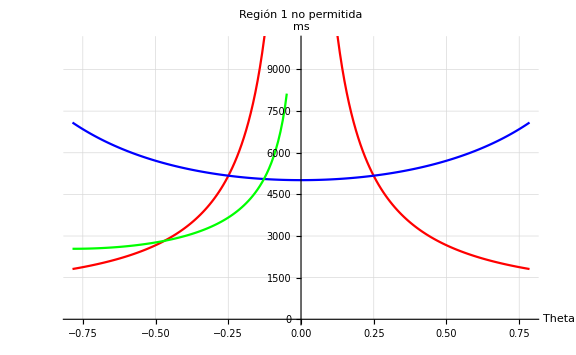

```mathematica
(*Definición de constantes*)mh=125;
v=256;
gchi=0.5;
mZp=1000;

(*Rango de valores para theta*)
thetaValues=Range[-Pi/4,Pi/4,Pi/400];

(*Resolver las desigualdades para cada valor de theta*)
msInvalidValues1=Table[Sqrt[(-1.0*mh^2*Cos[theta]^2+8*Pi*v^2)/Sin[theta]^2],{theta,thetaValues}];
msInvalidValues2=Table[Sqrt[(-gchi^2*mh^2*Sin[theta]^2+2*Pi*mZp^2)/(gchi^2*Cos[theta]^2)],{theta,thetaValues}];
msInvalidValues3=Table[If[(mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta]))>=0,Sqrt[mh^2-4*Pi*mZp*v/(gchi*Sin[2*theta])],Indeterminate],{theta,thetaValues}];

(*Plotting*)
upperLimit=1.5*Max[Max[msInvalidValues1],Max[msInvalidValues2],Max[msInvalidValues3]];

Show[ListLinePlot[{thetaValues,msInvalidValues1}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Red],PlotStyle->Red,PlotLabel->"Región 1 no permitida"],ListLinePlot[{thetaValues,msInvalidValues2}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Blue],PlotStyle->Blue,PlotLabel->"Región 2 no permitida"],ListLinePlot[{thetaValues,msInvalidValues3}//Transpose,Filling->{1->{upperLimit}},FillingStyle->Directive[Opacity[0.3],Green],PlotStyle->Green,PlotLabel->"Región 3 no permitida"],PlotRange->{{-Pi/4,Pi/4},{0,10000}},AxesLabel->{"Theta","ms"},GridLines->Automatic,ImageSize->Large]
```